## Creando una esfera a partir de discos

```mathematica
disk[n_,r_,h_]:={Yellow,EdgeForm[None],Cylinder[{{1,1,n*h},{1,1,n*h+h}},√(r^2-(n h)^2)]};HalfSphere[r_,n_]:=Table[disk[i,r,r/n],{i,n}];
```

```mathematica
gg=GraphicsGrid[{
{Graphics3D[HalfSphere[30,5]],Graphics3D[HalfSphere[30,7]],Graphics3D[HalfSphere[30,10]]},{Graphics3D[HalfSphere[30,15]],Graphics3D[HalfSphere[30,20]],Graphics3D[HalfSphere[30,50]]}
},ImageSize->800]
```

-Graphics-

```mathematica
Export["gg.jpg",gg]
```

gg.jpg

```mathematica
model=Graphics3D[HalfSphere[30,8]]
```

-Graphics3D-

```mathematica
SetDirectory["/Users/tomasdecaminobeck/Downloads/"]
```

/Users/tomasdecaminobeck/Downloads

```mathematica
Export["model8.stl",model]
```

model8.stl

```mathematica
Manipulate[Graphics3D[HalfSphere[30,n], PlotRange->{Automatic,Automatic,{0,30}}],{n,3,100}]
```

```mathematica
aprox[r_,n_]:=4 r/n∑_(i=1)^n √(r^2-(i/n r)^2);
```

Plot::exclul: {(1-i^2/n^2)-0,n-0,n-0,-Im[i^2/n^2]-0} must be a list of equalities or real-valued functions.

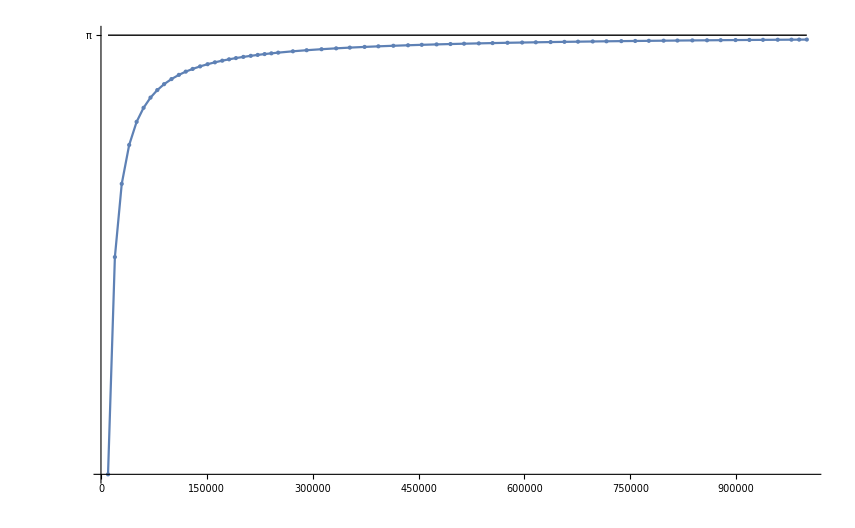

```mathematica
Show[Plot[aprox[1,n]//N,{n,10000,1000000},PlotRange->All,Mesh->All,MaxRecursion->1,Ticks->{ Automatic,{Pi}}],Graphics[Line[{{10000,Pi},{1000000,Pi}}]],LabelStyle->Large]
```